```mathematica
Numerics;
(* Import files for lambda/4 thickness at 615 nm (starting on substrate)*)

fiberlist = Import["/Users/ejanitz/Dropbox/McGill/Project/Cavity/Cavity Simulations/New Mirror Coating Simulations/fiber_coating.csv"];
flatslist = Import["/Users/ejanitz/Dropbox/McGill/Project/Cavity/Cavity Simulations/New Mirror Coating Simulations/flats_coating.csv"];

(* tables for thicknesses *)
fiberthick = Table[0,Length[fiberlist]];
flatsthick = Table[0,Length[flatslist]];
nfiber = Table[0,Length[fiberlist]];
nflats = Table[0,Length[flatslist]];

nhim = 3.1*10^-6;
nlim = 3.1*10^-6; 
ndim = 0*10^-6;
σd =1.5*10^-10;
λt = 615*10^-9;
c = 2.99792458*10^8;
R0=45*10^-6;

γ = 1/(6*10^-9);
γs =2*Pi*5.22*10^12;

dimplant = 125*10^-9;
dimplant1 = (125-20)*10^-9;
dimplant2 = (125+20)*10^-9;
dimplant11 = (125-40)*10^-9;
dimplant22 = (125+40)*10^-9;

Ed35p3 = 0.81613760507;
Ed54p7 = 0.57785762507; 

nh=2.125-I*nhim;
nl=1.482-I*nlim;
nd = 2.417-I*ndim;
na=1;
ns=1.4633;

M[n1_, n2_]:= ({{(Re[n1]+Re[n2])/(2 Re[n2]), (-Re[n1]+Re[n2])/(2 Re[n2])}, {(-Re[n1]+Re[n2])/(2 Re[n2]), (Re[n1]+Re[n2])/(2 Re[n2])}}); (* This is going from n1 into n2 *)

L[λ_,n_,d_]:={{Exp[-I*2*Pi*n*d/λ], 0},{0, Exp[I*2*Pi*n*d/λ]}}

Calculate air and diamond parameters;
r12[λ_,σ_]:=(Re[na]-Re[nd])/(Re[na]+Re[nd])*Exp[-2*(2*Pi*σ/λ)^2];
t12[λ_,σ_]:=2*Re[na]/(Re[na]+Re[nd])*Exp[-1/2*(2*Pi*σ*(1-Re[nd])/λ)^2];
r21[λ_,σ_]:=(Re[nd]-Re[na])/(Re[na]+Re[nd])*Exp[-2*(2*Pi*σ*Re[nd]/λ)^2];
t21[λ_,σ_]:=(2*Re[nd])/(Re[na]+Re[nd])*Exp[-1/2*(2*Pi*σ*(Re[nd]-1)/λ)^2];

r34[λ_,σ_]:=r21[λ,σ];
t34[λ_,σ_]:=t21[λ,σ];
r43[λ_,σ_]:=r12[λ,σ];
t43[λ_,σ_]:=t12[λ,σ];

Dad[λ_,σ_]:={{t12[λ,σ]-(r12[λ,σ]*r21[λ,σ])/t21[λ,σ], r21[λ,σ]/t21[λ,σ]},{-r12[λ,σ]/t21[λ,σ], 1/t21[λ,σ]}};
Dda[λ_,σ_]:={{t34[λ,σ]-(r34[λ,σ]*r43[λ,σ])/t43[λ,σ], r43[λ,σ]/t43[λ,σ]},{-r34[λ,σ]/t43[λ,σ], 1/t43[λ,σ]}};
```

1

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

7.15×10^-7

1.52521×10^9

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

Set::pkspec1: The expression j cannot be used as a part specification.

1.68163×10^-11

17899.3

flat field 3.98264×10^-14

fiber field 7.40155×10^-15

diamond and air field {7.0674×10^-14}{1.22989×10^-13}

2

7.3×10^-7

1.85925×10^9

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::stop: Further output of FindFit::sszero will be suppressed during this calculation.

Set::pkspec1: The expression j cannot be used as a part specification.

General::stop: Further output of Set::pkspec1 will be suppressed during this calculation.

2.75148×10^-11

10939.6

flat field 4.90853×10^-14

fiber field 5.00153×10^-15

diamond and air field {9.19074×10^-14}{6.84376×10^-14}

3

7.45×10^-7

1.65279×10^9

1.992×10^-11

15110.4

flat field 4.28082×10^-14

fiber field 6.42024×10^-15

diamond and air field {8.3567×10^-14}{8.19168×10^-14}

4

7.6×10^-7

1.29906×10^9

1.17721×10^-11

25568.9

flat field 2.97216×10^-14

fiber field 9.03045×10^-15

diamond and air field {5.87885×10^-14}{1.25285×10^-13}

5

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NMaximize::cvmit will be suppressed during this calculation.

7.75×10^-7

1.11157×10^9

8.86292×10^-12

33961.7

flat field 2.10095×10^-14

fiber field 1.00732×10^-14

diamond and air field {4.04474×10^-14}{1.47893×10^-13}

6

7.9×10^-7

1.04524×10^9

7.98349×10^-12

37702.8

flat field 1.76102×10^-14

fiber field 1.02311×10^-14

diamond and air field {3.15519×10^-14}{1.55846×10^-13}

7

8.05×10^-7

1.06131×10^9

8.19386×10^-12

36734.8

flat field 1.84309×10^-14

fiber field 1.01919×10^-14

diamond and air field {2.95225×10^-14}{1.59616×10^-13}

8

8.2×10^-7

1.16629×10^9

9.70518×10^-12

31014.4

flat field 2.37733×10^-14

fiber field 9.76499×10^-15

diamond and air field {3.33212×10^-14}{1.56288×10^-13}

9

8.35×10^-7

1.40178×10^9

1.4236×10^-11

21143.6

flat field 3.45541×10^-14

fiber field 8.01394×10^-15

diamond and air field {4.31174×10^-14}{1.2873×10^-13}

10

8.5×10^-7

1.71323×10^9

2.4978×10^-11

12050.6

flat field 4.60336×10^-14

fiber field 5.2534×10^-15

diamond and air field {5.49838×10^-14}{7.52737×10^-14}

11

8.65×10^-7

1.68874×10^9

2.36632×10^-11

12720.1

flat field 4.46163×10^-14

fiber field 5.42859×10^-15

diamond and air field {5.71568×10^-14}{5.38392×10^-14}

12

8.8×10^-7

1.39241×10^9

1.34648×10^-11

22354.6

flat field 3.23023×10^-14

fiber field 8.09033×10^-15

diamond and air field {4.92472×10^-14}{7.08237×10^-14}

13

8.95×10^-7

1.19072×10^9

9.43985×10^-12

31886.1

flat field 2.22132×10^-14

fiber field 9.55501×10^-15

diamond and air field {4.25155×10^-14}{8.5616×10^-14}

14

9.1×10^-7

1.10513×10^9

8.11874×10^-12

37074.7

flat field 1.75221×10^-14

fiber field 9.85884×10^-15

diamond and air field {4.22069×10^-14}{9.2129×10^-14}

15

9.25×10^-7

1.09835×10^9

8.02204×10^-12

37521.6

flat field 1.71238×10^-14

fiber field 9.85715×10^-15

diamond and air field {5.03609×10^-14}{9.6465×10^-14}

16

9.4×10^-7

1.16451×10^9

9.05306×10^-12

33248.4

flat field 2.08392×10^-14

fiber field 9.62835×10^-15

diamond and air field {7.13305×10^-14}{9.95194×10^-14}

17

9.55×10^-7

1.32694×10^9

1.23329×10^-11

24406.3

flat field 2.96787×10^-14

fiber field 8.42366×10^-15

diamond and air field {1.11662×10^-13}{9.35983×10^-14}

18

9.7×10^-7

1.57566×10^9

2.12792×10^-11

14145.3

flat field 4.17341×10^-14

fiber field 5.77239×10^-15

diamond and air field {1.62137×10^-13}{6.90351×10^-14}

19

9.85×10^-7

1.66209×10^9

2.6826×10^-11

11220.5

flat field 4.50823×10^-14

fiber field 4.73102×10^-15

diamond and air field {1.69448×10^-13}{4.67734×10^-14}

20

1.×10^-6

1.46313×10^9

1.57797×10^-11

19075.2

flat field 3.48612×10^-14

fiber field 7.03983×10^-15

diamond and air field {1.18913×10^-13}{4.34975×10^-14}

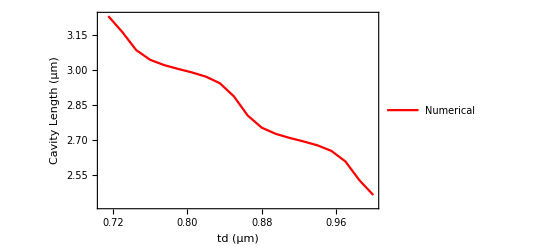

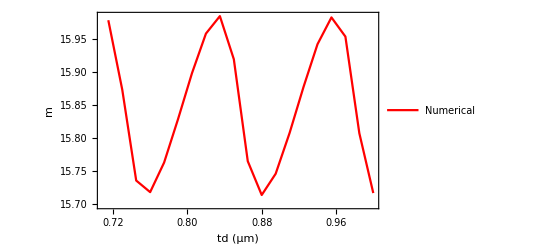

```mathematica
Calculating Mirror Reflectivities;

For[i=1,i<(Length[fiberlist])+1,i++,
	If[fiberlist[[i,2]]=="SiO2",n=nl,n=nh];
	fiberthick[[i]]=λt/(Re[n]*4)*fiberlist[[i,3]];
	nfiber[[i]]=n;
]

For[i=1,i<(Length[flatslist])+1,i++,
	If[flatslist[[i,2]]=="SiO2",n=nl,n=nh];
	flatsthick[[i]]=λt/(Re[n]*4)*flatslist[[i,3]];
	nflats[[i]] = n;
]

(* define wavelenth range for simulations*)
λtest=602*10^-9;
ftest = c/λtest;

mmax = 1;
kmax =100;
mtarget = 16;

tdmin =0.7*10^-6;
tdmax =1*10^-6;

tdvec = Table[tdmin+(tdmax-tdmin)*k/kmax,{k,kmax}];
Lvec = Table[0,{k,kmax}];
mvec = Table[0,{k,kmax}];
FSRvec =Table[0,{k,kmax}];
fwidthVec=Table[0,{k,kmax}];
EVec=Table[0,{k,kmax}];
normVec=Table[0,{k,kmax}];
Fpvec=Table[0,{k,kmax}];
Fpvec1=Table[0,{k,kmax}];
Fpvec2=Table[0,{k,kmax}];
Fpvec11=Table[0,{k,kmax}];
Fpvec22=Table[0,{k,kmax}];
RVec=Table[0,{k,kmax}];
RVec1=Table[0,{k,kmax}];
RVec2=Table[0,{k,kmax}];
RVec11=Table[0,{k,kmax}];
RVec22=Table[0,{k,kmax}];

gvec=Table[0,{k,kmax}];
gvec1=Table[0,{k,kmax}];
gvec2=Table[0,{k,kmax}];
gvec11=Table[0,{k,kmax}];
gvec22=Table[0,{k,kmax}];


Vvec=Table[0,{k,kmax}];
Vvec1=Table[0,{k,kmax}];
Vvec2=Table[0,{k,kmax}];
Vvec11=Table[0,{k,kmax}];
Vvec22=Table[0,{k,kmax}];

Evec=Table[0,{k,kmax}];
Evec1=Table[0,{k,kmax}];
Evec2=Table[0,{k,kmax}];
Evec11=Table[0,{k,kmax}];
Evec22=Table[0,{k,kmax}];

Mfiber= M[nh,ns];
	For[i=1,i<(Length[fiberlist])+1,i++,
		If[fiberlist[[i,2]]=="SiO2",Mfiber=Simplify[Mfiber.L[λtest,nfiber[[i]],fiberthick[[i]]].M[nh,nl]]];
		If[fiberlist[[i,2]]=="Ta2O5" && i≠Length[fiberlist],Mfiber=Simplify[Mfiber.L[λtest,nfiber[[i]],fiberthick[[i]]].M[nl,nh]]];
		If[fiberlist[[i,2]]=="Ta2O5" && i==Length[fiberlist],Mfiber=Simplify[Mfiber.L[λtest,nfiber[[i]],fiberthick[[i]]].M[na,nh]]];
	];

	Mflatsinv= M[nl,na];
	For[i=Length[flatslist],i>0,i--,
		If[flatslist[[i,2]]=="SiO2",Mflatsinv=Simplify[Mflatsinv.L[λtest,nflats[[i]],flatsthick[[i]]].M[nh,nl]]];
		If[flatslist[[i,2]]=="Ta2O5" && i≠1,Mflatsinv=Simplify[Mflatsinv.L[λtest,nflats[[i]],flatsthick[[i]]].M[nl,nh]]];
		If[flatslist[[i,2]]=="Ta2O5" && i==1,Mflatsinv=Simplify[Mflatsinv.L[λtest,nflats[[i]],flatsthick[[i]]].M[ns,nh]]];
	];

For[k=1,k<kmax+1,k++,(* here i'm iterating over diamond thickness td - λtest is fixed *)

	Print[k];
	(* starting guess for length *)
	Lmin =(mtarget+1/2)*λtest/2-(nd-1)*tdvec[[k]];

	Stest[Ltest_,λ_] := Mfiber.L[λ,na,(Ltest-tdvec[[k]])].Dda[λtest,σd].L[λ,nd,tdvec[[k]]].Dad[λtest,σd].Mflatsinv;
          (*  this is the transmitted field Z1 *)
	Gtest[Ltest_,freq_] := Stest[Ltest,c/freq][[1,1]]-Stest[Ltest,c/freq][[1,2]]*Stest[Ltest,c/freq][[2,1]]/Stest[Ltest,c/freq][[2,2]];
	(*  calculate the reflected field A2 *)
	A2test[Ltest_,freq_]:=-Stest[Ltest,c/freq][[2,1]]/Stest[Ltest,c/freq][[2,2]];

	(* find resonance *)
	Ltest = L/.NMaximize[Abs[FullSimplify[Gtest[L,ftest]]]^2,{L,Lmin-λtest/4,Lmin}][[2]];

	(* Print["this is resonant reflection ",Abs[A2test[Ltest,ftest]]^2];
	Print["this is resonant transmission ",Abs[Gtest[Ltest,ftest]]^2]; *)
	
	(* populate length and m vector *)
	Lvec[[k]]=Ltest;	
	mvec[[k]]=2*((nd-1)*tdvec[[k]]+Ltest)/λtest-1/2;

	(* now in frequency *)
	FSRtest = c/(2*(Ltest-tdvec[[k]]+Re[nd]*tdvec[[k]]));
	fHighF = Table[i,{i,ftest-FSRtest/2000,ftest+FSRtest/2000,FSRtest/1000000}];
	fTHigh = Table[Abs[Gtest[Ltest,i]]^2,{i,ftest-FSRtest/2000,ftest+FSRtest/2000,FSRtest/1000000}];
	fHighFDat = Transpose[{fHighF,fTHigh}];
	(*Print[ListLinePlot[Transpose[{(fHighF-λtest)*10^9,fTHigh}],PlotRange->Full,AxesLabel->{"laser wavelength (nm)","T"}]];*)

	af=Max[fTHigh]-Min[fTHigh]; (* amplitude *)
	yf = Min[fTHigh]; (* offset *)
	x0f = fHighF[[( Position[fTHigh,Max[fTHigh]][[1]])[[1]]]]; (* center position *)
	bguessf = 2*Abs[x0f-fHighF[[(Position[fTHigh,Nearest[fTHigh,Min[fTHigh]+af/2][[1]]][[1]])[[1]]]]]; (* guess at width*)

	fFit = a*(b/2)^2/((x-x0)^2+(b/2)^2)+y;
	fpeakW  = Quiet[b/. FindFit[fHighFDat,fFit,{{b,bguessf},{x0,x0f},{a,af},{y,yf}},x][[1]]];
	fwidthVec[[k]] = fpeakW;
	fTHighFit = Table[af*(fpeakW/2)^2/((fHighF[[i]]-x0f)^2+(fpeakW/2)^2)+yf,{i,Length[fHighF]}];

	FSRmin = f/.NMaximize[{Abs[FullSimplify[Gtest[Ltest,f]]]^2,f>x0f-1.6*FSRtest&&f<x0f-0.4*FSRtest},f][[2]];
	FSRmax = f/.NMaximize[{Abs[FullSimplify[Gtest[Ltest,f]]]^2,f>x0f+0.4*FSRtest&&f<x0f+1.6*FSRtest},f][[2]];
	FSRvec[[k]]= ((fpeakW-FSRmin)+(FSRmax-fpeakW))/2;
	(* Print[Plot[Abs[Gtest[Ltest,f]]^2,{f,x0f-1.5*FSRtest,x0f+1.5*FSRtest},PlotRange->Full]];  *)	(*Print[ListLinePlot[{ Transpose[{(fHighF-x0f),fTHigh}],Transpose[{(fHighF-x0f),fTHighFit}]},PlotRange->Full,    PlotLabel->"Resonance in frequency",AxesLabel->{"f (Hz)","T"}]]; *)
Print[tdvec[[k]]];
Print[fpeakW];

		(* finesse in length *)
		lHighF = Table[i,{i,Ltest-λtest/2/5000,Ltest+λtest/2/5000,λtest/2/1000000}];
		lTHigh = Table[Abs[Gtest[i,ftest]]^2,{i,Ltest-λtest/2/5000,Ltest+λtest/2/5000,λtest/2/1000000}];
		lHighFDat = Transpose[{lHighF,lTHigh}];
	
		(* first in length*)
		al=Max[lTHigh]-Min[lTHigh]; (* amplitude *)
		yl = Min[lTHigh]; (* offset *)
		x0l = lHighF[[( Position[lTHigh,Max[lTHigh]][[1]])[[1]]]]; (* center position *)
		bguessl = 2*Abs[x0l-lHighF[[(Position[lTHigh,Nearest[lTHigh,Min[lTHigh]+al/2][[1]]][[1]])[[1]]]]]; (* guess at width*)

		lFit = a*(b/2)^2/((x-x0)^2+(b/2)^2)+y;
		lpeakW  = b/. FindFit[lHighFDat,lFit,{{b,bguessl},{x0,x0l},{a,al},{y,yl}},x][[1]];
		Ltest = x0/.FindFit[lHighFDat,lFit,{{x0,x0l},{b,bguessl},{a,al},{y,yl}},x][[1]];
		Lvec[[j]]=Ltest;
		lwidthVec[[j]] = lpeakW;
                     Print[lpeakW];
		lTHighFit = Table[al*(lpeakW/2)^2/((lHighF[[i]]-Ltest)^2+(lpeakW/2)^2)+yl,{i,Length[lHighF]}];		(*Print[ListLinePlot[{ Transpose[{(lHighF-Ltest)*10^9,lTHigh}],Transpose[{(lHighF-Ltest)*10^9,lTHighFit}]},PlotRange->Full,AxesLabel->{"cavity length (nm)","T"},PlotLabel->N[λtest*10^9]]]; *)
	Print[λtest/2/lpeakW];

	z02=td*(1-1/nd)/.λ->c/ν/.ta->(L-td)/.{td->tdvec[[k]],L->Ltest,ν->ftest};
	w01= Sqrt[λ/Pi]*((ta+td/nd)*(R0-(ta+td/nd)))^(1/4)/.λ->c/ν/.ta->(L-td)/.{td->tdvec[[k]],L->Ltest,ν->ftest};

	(* determine electric field in diamond *)
	Evals =Dda[λtest,σd].L[λtest,nd,tdvec[[k]]].Dad[λtest,σd].Mflatsinv .{{1},{A2test[Ltest,ftest] }};
	E1 =Evals[[1]];
	E2 = Evals[[2]];
	
	Dvals =L[λtest,nd,tdvec[[k]]].Dad[λtest,σd].Mflatsinv.{{1 },{A2test[Ltest,ftest] }};
	D1 =Dvals[[1]];
	D2 = Dvals[[2]];
	
	Cvals = Dad[λtest,σd].Mflatsinv.{{1 },{A2test[Ltest,ftest] }};
	C1 =Cvals[[1]];
	C2 = Cvals[[2]];

	(* Evals =Dda[λtest,σd].L[λtest,nd,tdvec[[k]]].Dad[λtest,σd].Mflatsinv .{{1},{0}};
	E1 =Evals[[1]];
	E2 = Evals[[2]];
	
	Dvals =L[λtest,nd,tdvec[[k]]].Dad[λtest,σd].Mflatsinv.{{1 },{0}};
	D1 =Dvals[[1]];
	D2 = Dvals[[2]];
	
	Cvals = Dad[λtest,σd].Mflatsinv.{{1 },{0}};
	C1 =Cvals[[1]];
	C2 = Cvals[[2]]; *)

	(* Determine the max electric field in diamond *)
	(*dEfield = Max[Table[Re[C1*ⅇ^(-ⅈ x*(2*π*nd/λtest))+C2*ⅇ^(+ⅈ x*(2*π*nd/λtest))][[1]],{x,0,tdvec[[k]],tdvec[[k]]/10000}]];*)
	dEfield = Abs[Re[(C1*ⅇ^(-ⅈ dimplant*(2*π*nd/λtest))+C2*ⅇ^(+ⅈ dimplant*(2*π*nd/λtest)))][[1]]];
	dEfield1 = Min[Abs[Table[Re[C1*ⅇ^(-ⅈ x*(2*π*nd/λtest))+C2*ⅇ^(+ⅈ x*(2*π*nd/λtest))][[1]],{x,dimplant1,dimplant2,tdvec[[k]]/10000}]]];
	dEfield2 = Max[Abs[Table[Re[C1*ⅇ^(-ⅈ x*(2*π*nd/λtest))+C2*ⅇ^(+ⅈ x*(2*π*nd/λtest))][[1]],{x,dimplant1,dimplant2,tdvec[[k]]/10000}]]];
	dEfield11 = Min[Abs[Table[Re[C1*ⅇ^(-ⅈ x*(2*π*nd/λtest))+C2*ⅇ^(+ⅈ x*(2*π*nd/λtest))][[1]],{x,dimplant11,dimplant22,tdvec[[k]]/10000}]]];
	dEfield22 = Max[Abs[Table[Re[C1*ⅇ^(-ⅈ x*(2*π*nd/λtest))+C2*ⅇ^(+ⅈ x*(2*π*nd/λtest))][[1]],{x,dimplant11,dimplant22,tdvec[[k]]/10000}]]];
	(*dEfield1 = Re[(C1*ⅇ^(-ⅈ dimplant1*(2*π*nd/λtest))+C2*ⅇ^(+ⅈ dimplant1*(2*π*nd/λtest)))][[1]];
	dEfield2 = Re[(C1*ⅇ^(-ⅈ dimplant2*(2*π*nd/λtest))+C2*ⅇ^(+ⅈ dimplant2*(2*π*nd/λtest)))][[1]];*)
	EVec[[k]] = dEfield; *)

	field100 = Re[nd]^2*Re[Quiet[NIntegrate[(Re[C1*ⅇ^(-ⅈ x*(2*π*nd/λtest))+C2*ⅇ^(ⅈ x*(2*π*nd/λtest))])^2*Pi*w01^2/2,{x,0,tdvec[[k]]},AccuracyGoal->8]]];
	field200 = Re[Quiet[NIntegrate[(Re[E1*ⅇ^(-ⅈ( x-tdvec[[k]])*(2*π/λtest))+E2*ⅇ^(ⅈ (x-tdvec[[k]])*(2*π/λtest))])^2*Pi*w01^2/2,{x,tdvec[[k]],Ltest},AccuracyGoal->8]]];

	(* I need to add a section where I integrate the field inside the mirror coatings... *)
	fieldflat = 0;
(* start at high index terminated first layer from substrate *)
	Aflat =M[ns,nh].{{1 },{A2test[Ltest,ftest] }};	
	For[i=1,i<(Length[flatslist])+1,i++,
fieldflat = fieldflat + Re[Re[nflats[[i]]]]^2*Re[Quiet[NIntegrate[(Re[Aflat[[1]]*ⅇ^(-ⅈ x*(2*π*Re[nflats[[i]]]/λtest))+Aflat[[2]]*ⅇ^(ⅈ x*(2*π*Re[nflats[[i]]]/λtest))])^2*Pi*w01^2/2,{x,0,flatsthick[[i]]},AccuracyGoal->8]]][[1]];

		If[flatslist[[i,2]]=="SiO2",
			Aflat = M[nl,nh].L[λtest,Re[nflats[[i]]],flatsthick[[i]]].Aflat];
		If[flatslist[[i,2]]=="Ta2O5" && i≠Length[flatslist],
			Aflat = M[nh,nl].L[λtest,Re[nflats[[i]]],flatsthick[[i]]].Aflat];
		];

	Afiber = M[ns,nh].{{Gtest[Ltest,ftest]},{0}};
	fieldfiber = 0;
	For[i=1,i<(Length[fiberlist])+1,i++,
fieldfiber= fieldfiber+ Re[Re[nfiber[[i]]]]^2*Re[Quiet[NIntegrate[(Re[Afiber[[1]]*ⅇ^(-ⅈ x*(2*π*Re[nfiber[[i]]]/λtest))+Afiber[[2]]*ⅇ^(ⅈ x*(2*π*Re[nfiber[[i]]]/λtest))])^2*Pi*w01^2/2,{x,0,fiberthick[[i]]},AccuracyGoal->8]]][[1]];
		If[fiberlist[[i,2]]=="SiO2",Afiber = M[nl,nh].L[λtest,Re[nfiber[[i]]],fiberthick[[i]]].Afiber];
		If[fiberlist[[i,2]]=="Ta2O5" && i≠Length[fiberlist],Afiber = M[nh,nl].L[λtest,Re[nfiber[[i]]],fiberthick[[i]]].Afiber];
		
	];

	norm00 = field100+field200+fieldflat+fieldfiber;
	normVec[[k]] = norm00[[1]];

	V = norm00/(Re[nd]^2*Abs[dEfield]^2);
	V1 = norm00/(Re[nd]^2*Abs[dEfield1]^2);
	V2 = norm00/(Re[nd]^2*Abs[dEfield2]^2);
	V11 = norm00/(Re[nd]^2*Abs[dEfield11]^2);
	V22 = norm00/(Re[nd]^2*Abs[dEfield22]^2);
	Q=c/(λtest*fpeakW);
	gtest = Sqrt[(3*c*γ*λtest^2)/(8*Pi*Re[nd]^3*V)][[1]];
	gtest1 = Sqrt[(3*c*γ*λtest^2)/(8*Pi*Re[nd]^3*V1)][[1]];
	gtest2 = Sqrt[(3*c*γ*λtest^2)/(8*Pi*Re[nd]^3*V2)][[1]];
	gtest11 = Sqrt[(3*c*γ*λtest^2)/(8*Pi*Re[nd]^3*V11)][[1]];
	gtest22 = Sqrt[(3*c*γ*λtest^2)/(8*Pi*Re[nd]^3*V22)][[1]];

	(*Fpvec[[k]]=4*gtest^2/(γ*2*Pi*fpeakW);
	Fpvec1[[k]]=4*gtest1^2/(γ*2*Pi*fpeakW);
	Fpvec2[[k]]=4*gtest2^2/(γ*2*Pi*fpeakW);*)

	Fpvec[[k]]=3/(4*Pi^2)*(λtest/nd)^3*(Q/V);
	Fpvec1[[k]]=3/(4*Pi^2)*(λtest/nd)^3*(Q/V1);
	Fpvec2[[k]]=3/(4*Pi^2)*(λtest/nd)^3*(Q/V2);
	Fpvec11[[k]]=3/(4*Pi^2)*(λtest/nd)^3*(Q/V11);
	Fpvec22[[k]]=3/(4*Pi^2)*(λtest/nd)^3*(Q/V22);

	gvec[[k]]=gtest;
	gvec1[[k]]=gtest1;
	gvec2[[k]]=gtest2;
	gvec11[[k]]=gtest11;
	gvec22[[k]]=gtest22;


	Vvec[[k]]=V;
	Vvec1[[k]]=V1;
	Vvec2[[k]]=V2;
	Vvec11[[k]]=V11;
	Vvec22[[k]]=V22;

	Evec[[k]]=dEfield;
	Evec1[[k]]=dEfield1;
	Evec2[[k]]=dEfield2;
	Evec11[[k]]=dEfield11;
	Evec22[[k]]=dEfield22;

	RVec[[k]]=4*gtest^2/γs;
	RVec1[[k]]=4*gtest1^2/γs;
	RVec2[[k]]=4*gtest2^2/γs;
	RVec11[[k]]=4*gtest11^2/γs;
	RVec22[[k]]=4*gtest22^2/γs;


];
 
ListLinePlot[{Transpose[{tdvec*10^6,(Lvec-tdvec)*10^6}]},AxesLabel->{"td","ta"},Frame->True,BaseStyle->{FontFamily->"Arial",FontSize->14},(*PlotMarkers->{Automatic,12},*)FrameLabel->{"td (μm)","Cavity Length (μm)"},FrameStyle->{Black,Directive[Black,FontColor->Black]},PlotStyle->Red,PlotLegends->{"Numerical"}] 

ListLinePlot[{Transpose[{tdvec*10^6,mvec}]},AxesLabel->{"laser λ (nm)","cavity L (um)"},Frame->True,BaseStyle->{FontFamily->"Arial",FontSize->14},(*PlotMarkers->{Automatic,12},*)FrameLabel->{"td (μm)","m"},FrameStyle->{Black,Directive[Black,FontColor->Black]},PlotStyle->Red,PlotLegends->{"Numerical"}] 

(*ListLinePlot[{Transpose[{tdvec*10^6,βVec*100}],Transpose[{tdvec*10^6,βVec1*100}],Transpose[{tdvec*10^6,βVec2*100}]},Frame->True,BaseStyle->{FontFamily->"Arial",FontSize->14},(*PlotMarkers->{Automatic,12},*)FrameLabel->{"td (μm)","β (%)"},FrameStyle->{Black,Directive[Black,FontColor->Black]},PlotLegends->{"target","-straggle","+straggle"}] *)
```

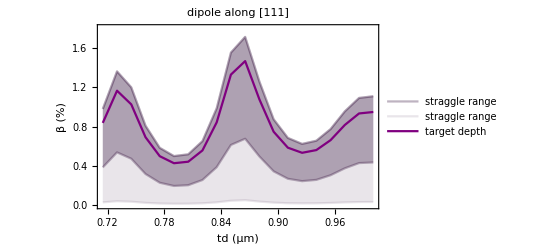

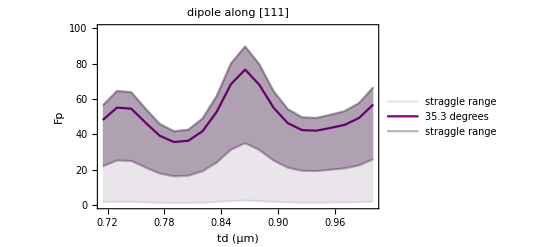

```mathematica
p35p3 = ListLinePlot[{Transpose[{tdvec*10^6,(0.6*RVec1*(Ed35p3)^2/(0.6*RVec1*(Ed35p3)^2+γ))*100}],Transpose[{tdvec*10^6,(0.6*RVec2*(Ed35p3)^2/(0.6*RVec2*(Ed35p3)^2+γ))*100}]},Filling->{1->{2}},FillingStyle->{Hue[0.8,0.9,0.2,0.3]},PlotStyle->{Hue[0.8,0.9,0.2,0.3]},Frame->True,BaseStyle->{FontFamily->"Arial",FontSize->14},FrameLabel->{"td (μm)","β (%)"},FrameStyle->{Black,Directive[Black,FontColor->Black]},PlotRange->{{Min[tdvec]*10^6,Max[tdvec]*10^6},{0,1.8}},PlotLabel->"dipole along [111]",PlotLegends->{"straggle range"}];

p35p3p2 = ListLinePlot[{Transpose[{tdvec*10^6,(0.6*RVec11*(Ed35p3)^2/(0.6*RVec11*(Ed35p3)^2+γ))*100}],Transpose[{tdvec*10^6,(0.6*RVec22*(Ed35p3)^2/(0.6*RVec22*(Ed35p3)^2+γ))*100}]},Filling->{1->{2}},FillingStyle->{Hue[0.8,0.9,0.2,0.1]},PlotStyle->{Hue[0.8,0.9,0.2,0.1]},Frame->True,BaseStyle->{FontFamily->"Arial",FontSize->14},FrameLabel->{"td (μm)","β (%)"},FrameStyle->{Black,Directive[Black,FontColor->Black]},PlotRange->{{Min[tdvec]*10^6,Max[tdvec]*10^6},{0,2.6}},PlotLabel->"dipole along [111]",PlotLegends->{"straggle range"}];

p35p3line = ListLinePlot[{Transpose[{tdvec*10^6,(0.6*RVec*(Ed35p3)^2/(0.6*RVec*(Ed35p3)^2+γ))*100}]},PlotLegends->{"target depth"},PlotStyle->{{Purple,Thick},{Purple,Thick}},PlotRange->{{0.7,1},{0,3.2}}];

pplane = ListLinePlot[{Transpose[{tdvec*10^6,(0.6*RVec/(0.6*RVec+γ))*100}],Transpose[{tdvec*10^6,(0.6*RVec*(Ed54p7)^2/(0.6*RVec*(Ed54p7)^2+γ))*100}]},Filling->{1->{2}},FillingStyle->{Hue[0.1,0.95,0.949,0.9]},PlotStyle->{Hue[0.1,0.95,0.949,0.9]},Frame->True,BaseStyle->{FontFamily->"Arial",FontSize->14},FrameLabel->{"td (μm)","β (%)"},FrameStyle->{Black,Directive[Black,FontColor->Black]},PlotRange->{{Min[tdvec]*10^6,Max[tdvec]*10^6},{0,4.5}},{PlotLabel->"dipole in plane perp to [111]"},PlotLegends->{"Target depth"}];

pprangeplane = ListLinePlot[{Transpose[{tdvec*10^6,(0.6*RVec2/(0.6*RVec2+γ))*100}],Transpose[{tdvec*10^6,(0.6*RVec1*(Ed54p7)^2/(0.6*RVec1*(Ed54p7)^2+γ))*100}]},Filling->{1->{2}},FillingStyle->{Hue[0.1,0.95,0.949,0.3]},Frame->True,BaseStyle->{FontFamily->"Arial",FontSize->14},FrameLabel->{"td (μm)","β (%)"},FrameStyle->{Black,Directive[Black,FontColor->Black]},PlotRange->{{Min[tdvec]*10^6,Max[tdvec]*10^6},{0,4.5}},PlotLegends->{"Straggle range"},PlotStyle->Hue[0.1,0.95,0.949,0.3]];

Fp35p3line =ListLinePlot[{Transpose[{tdvec*10^6,Flatten[Fpvec]*(Ed35p3)^2}]},Frame->True,BaseStyle->{FontFamily->"Arial",FontSize->14},FrameLabel->{"td (μm)","Fp"},FrameStyle->{Black,Directive[Black,FontColor->Black]},PlotStyle->{{Purple,Thick}},PlotLegends->{"35.3 degrees"},PlotRange->{{Min[tdvec]*10^6,Max[tdvec]*10^6},{0,100}}];

Fp35p3 =ListLinePlot[{Transpose[{tdvec*10^6,Flatten[Fpvec1]*(Ed35p3)^2}],Transpose[{tdvec*10^6,Flatten[Fpvec2]*(Ed35p3)^2}]},Frame->True,BaseStyle->{FontFamily->"Arial",FontSize->14},FrameLabel->{"td (μm)","Fp"},FrameStyle->{Black,Directive[Black,FontColor->Black]},PlotStyle->{Hue[0.8,0.9,0.2,0.3]},PlotRange->{{Min[tdvec]*10^6,Max[tdvec]*10^6},{0,140}},Filling->{1->{2}},FillingStyle->{Hue[0.8,0.9,0.2,0.3]},PlotLabel->"dipole along [111]",PlotLegends->{"straggle range"}];

Fp35p3p2 =ListLinePlot[{Transpose[{tdvec*10^6,Flatten[Fpvec11]*(Ed35p3)^2}],Transpose[{tdvec*10^6,Flatten[Fpvec22]*(Ed35p3)^2}]},Frame->True,BaseStyle->{FontFamily->"Arial",FontSize->14},FrameLabel->{"td (μm)","Fp"},FrameStyle->{Black,Directive[Black,FontColor->Black]},PlotStyle->{Hue[0.8,0.9,0.2,0.1]},PlotRange->{{Min[tdvec]*10^6,Max[tdvec]*10^6},{0,100}},Filling->{1->{2}},FillingStyle->{Hue[0.8,0.9,0.2,0.1]},PlotLabel->"dipole along [111]",PlotLegends->{"straggle range"}];

Fpplane = ListLinePlot[{Transpose[{tdvec*10^6,Flatten[Fpvec]}],Transpose[{tdvec*10^6,Flatten[Fpvec]*(Ed54p7)^2}]},Filling->{1->{2}},FillingStyle->{Hue[0.1,0.95,0.949,0.9]},PlotStyle->{Hue[0.1,0.95,0.949,0.9]},Frame->True,BaseStyle->{FontFamily->"Arial",FontSize->14},FrameLabel->{"td (μm)","Fp"},FrameStyle->{Black,Directive[Black,FontColor->Black]},{PlotLabel->"dipole in plane perp to [111]"},PlotLegends->{"Target depth"},PlotRange->{{Min[tdvec]*10^6,Max[tdvec]*10^6},{0,200}}];

Fpprangeplane = ListLinePlot[{Transpose[{tdvec*10^6,Flatten[Fpvec2]}],Transpose[{tdvec*10^6,Flatten[Fpvec1]*(Ed54p7)^2}]},Filling->{1->{2}},FillingStyle->{Hue[0.1,0.95,0.949,0.3]},Frame->True,BaseStyle->{FontFamily->"Arial",FontSize->14},FrameLabel->{"td (μm)","Fp"},FrameStyle->{Black,Directive[Black,FontColor->Black]},PlotLegends->{"Straggle range"},PlotStyle->Hue[0.1,0.95,0.949,0.3]];

Show[p35p3,p35p3p2,p35p3line]
Show[Fp35p3p2,Fp35p3line,Fp35p3]
(* Show[pplane,pprangeplane]
Show[Fpplane,Fpprangeplane]*)
```

```mathematica
flatsthick
nflats
```

{8.53553×10^-8,1.59784×10^-7,9.47835×10^-8,4.45156×10^-8,2.88227×10^-8,1.10814×10^-7,8.55121×10^-8,1.44839×10^-7,1.16221×10^-7,1.18071×10^-7,1.20714×10^-7,1.06474×10^-7,5.13167×10^-8,5.51024×10^-8,7.65603×10^-8,1.09985×10^-7,7.86593×10^-8,1.10903×10^-7,7.7467×10^-8,1.07457×10^-7,7.1998×10^-8,9.9832×10^-8,6.86268×10^-8,1.02355×10^-7,7.10434×10^-8,1.06328×10^-7,7.1965×10^-8,1.08577×10^-7,7.15961×10^-8,1.12129×10^-7,6.88045×10^-8,1.20974×10^-7,5.73388×10^-8,1.38709×10^-7,3.64789×10^-8,1.51903×10^-7,4.19511×10^-8,1.59046×10^-7,4.17183×10^-8,1.65094×10^-7,3.63878×10^-8,1.64002×10^-7,3.30857×10^-8,1.63417×10^-7,3.20086×10^-8,1.74374×10^-7,2.37347×10^-8,1.99016×10^-7,8.18276×10^-9,1.42822×10^-7}

{2.125-3.1×10^-6 ⅈ,1.482-3.1×10^-6 ⅈ,2.125-3.1×10^-6 ⅈ,1.482-3.1×10^-6 ⅈ,2.125-3.1×10^-6 ⅈ,1.482-3.1×10^-6 ⅈ,2.125-3.1×10^-6 ⅈ,1.482-3.1×10^-6 ⅈ,2.125-3.1×10^-6 ⅈ,1.482-3.1×10^-6 ⅈ,2.125-3.1×10^-6 ⅈ,1.482-3.1×10^-6 ⅈ,2.125-3.1×10^-6 ⅈ,1.482-3.1×10^-6 ⅈ,2.125-3.1×10^-6 ⅈ,1.482-3.1×10^-6 ⅈ,2.125-3.1×10^-6 ⅈ,1.482-3.1×10^-6 ⅈ,2.125-3.1×10^-6 ⅈ,1.482-3.1×10^-6 ⅈ,2.125-3.1×10^-6 ⅈ,1.482-3.1×10^-6 ⅈ,2.125-3.1×10^-6 ⅈ,1.482-3.1×10^-6 ⅈ,2.125-3.1×10^-6 ⅈ,1.482-3.1×10^-6 ⅈ,2.125-3.1×10^-6 ⅈ,1.482-3.1×10^-6 ⅈ,2.125-3.1×10^-6 ⅈ,1.482-3.1×10^-6 ⅈ,2.125-3.1×10^-6 ⅈ,1.482-3.1×10^-6 ⅈ,2.125-3.1×10^-6 ⅈ,1.482-3.1×10^-6 ⅈ,2.125-3.1×10^-6 ⅈ,1.482-3.1×10^-6 ⅈ,2.125-3.1×10^-6 ⅈ,1.482-3.1×10^-6 ⅈ,2.125-3.1×10^-6 ⅈ,1.482-3.1×10^-6 ⅈ,2.125-3.1×10^-6 ⅈ,1.482-3.1×10^-6 ⅈ,2.125-3.1×10^-6 ⅈ,1.482-3.1×10^-6 ⅈ,2.125-3.1×10^-6 ⅈ,1.482-3.1×10^-6 ⅈ,2.125-3.1×10^-6 ⅈ,1.482-3.1×10^-6 ⅈ,2.125-3.1×10^-6 ⅈ,1.482-3.1×10^-6 ⅈ}